# Transversity Parameterization

## MSTW2008NLO

### Parameterization from eqns 6-12 of 0901.0002

```mathematica
xuv = Au x^η1(1-x)^η2(1+ϵu Sqrt[x]+γu x);
xdv = Ad x^η3(1-x)^η4(1+ϵd Sqrt[x]+γd x);
xSS = AS x^δS(1-x)^ηS(1+ϵS Sqrt[x]+γS x);
xΔΔ = AΔ x^ηΔ(1-x)^(ηS+2)(1+γΔ Sqrt[x]+δΔ x);
xsp = Ap x^δS(1-x)^ηp(1+ϵS Sqrt[x]+γS x);
xsm = Am x^δm(1-x)^ηm(1-x/x0);
```

### Parameters from Table 4 of 0901.0002 (Don’t run this block)

```mathematica
Au = 0.258710
η1 = 0.290650
η2 =3.243200
ϵu =4.060300
γu=30.68700

Ad=12.28800
η3=0.968090
η4=2.700300+η2
ϵd=-3.891100
γd=6.054200

AS=0.316200
δS=-0.215150
ηS=9.272600
ϵS=-2.602200
γS=30.78500

ID=0.087673
AΔ=8.108400
ηΔ=1.869100
γΔ=13.60900
δΔ=-59.28900

Ap=0.047915
ηp=9.746600
Am=-0.011629
ηm=11.26100
δm=0.200000
x0=0.016050
```

### Obtain the distribution functions from the parameterization

```mathematica
solns = Solve[{xuv == xuu-xub,xdv == xdd-xdb,xSS == 2(xub+xdb)+xss+xsb,xsp == xss+xsb,xsm == xss-xsb,xΔΔ == xdb-xub}, {xuu,xdd,xss,xsb,xub,xdb}];
XUUf = xuu/.solns[[1]];
XDDf = xdd/.solns[[1]];
XSSf = xss/.solns[[1]];
XUBf = xub/.solns[[1]];
{{XDBf = xdb/.solns[[1]];}, {XSBf = xsb/.solns[[1]];}}
```

{{Null},{Null}}

## DSSV

### Parameterization from eqns 28 of 0904.3821

```mathematica
xupg = Nup x^αup(1-x)^βup(1+γup Sqrt[x]+ηup x);
xdpg = Ndp x^αdp(1-x)^βdp(1+γdp Sqrt[x]+ηdp x);
xubg = Nub x^αub(1-x)^βub(1+γub Sqrt[x]+ηub x);
xdbg = Ndb x^αdb(1-x)^βdb(1+γdb Sqrt[x]+ηdb x);
xssg = Nss x^αss(1-x)^βss(1+γss Sqrt[x]+ηss x);
```

### Parameters from Table II of 0904.3821 (Don’t run this block)

```mathematica
Nup = 0.677
αup = 0.692
βup = 3.34
γup = -2.18
ηup = 15.87

Ndp = -0.015
αdp = 0.164
βdp = 3.89
γdp = 22.40
ηdp = 98.94

Nub = 0.295
αub = 0.692
βub = 10.
γub = 0.
ηub = -8.42

Ndb = -0.012
αdb = 0.164
βdb = 10.
γdb = 0.
ηdb = 98.94

Nss = -0.025
αss = 0.164
βss = 10.
γss = 0.
ηss = -29.52
```

### Obtain the distribution functions from the parameterization

```mathematica
solns = Solve[{xupg == xuug+xubg,xdpg == xddg+xdbg}, {xuug,xddg}];
XUUg = xuug/.solns[[1]];
XDDg = xddg/.solns[[1]];
XUBg = xubg;
XDBg = xdbg;
XSSg = xssg;
XSBg = xssg;
```

## CDKT

### Parameterization at Q0 = 1 GeV

```mathematica
CDKTuu = (NuuT x^(αuuT-1)(1-x)^βuuT(αuuT+βuuT)^(αuuT+βuuT)/((αuuT)^αuuT(βuuT)^βuuT)*1/2(XUUf+XUUg))//Expand;
CDKTdd =(NddT x^(αddT-1)(1-x)^βddT(αddT+βddT)^(αddT+βddT)/((αddT)^αddT(βddT)^βddT)*1/2(XDDf+XDDg))//Expand;
CDKTss = (NssT x^(αssT-1)(1-x)^βssT(αssT+βssT)^(αssT+βssT)/((αssT)^αssT(βssT)^βssT)*1/2(XSSf+XSSg))//Expand;
CDKTub =( NubT x^(αubT-1)(1-x)^βubT(αubT+βubT)^(αubT+βubT)/((αubT)^αubT(βubT)^βubT)*1/2(XUBf+XUBg))//Expand;
CDKTdb =(NdbT x^(αdbT-1)(1-x)^βdbT(αdbT+βdbT)^(αdbT+βdbT)/((αdbT)^αdbT(βdbT)^βdbT)*1/2(XDBf+XDBg))//Expand;
CDKTsb = (NsbT x^(αsbT-1)(1-x)^βsbT(αsbT+βsbT)^(αsbT+βsbT)/((αsbT)^αsbT(βsbT)^βsbT)*1/2(XSBf+XSBg))//Expand;
```

### Mellin Transformations

```mathematica
assumptions = {};
For[i=1,i≤Length[CDKTuu],i+=1,AppendTo[assumptions,Integrate[x^(n-1)Part[CDKTuu,i],{x,0,1}][[2]]]]
assumptions = Reduce[assumptions]
MellCDKTuu = 0;
For[i=1,i≤Length[CDKTuu],i+=1,MellCDKTuu+=Integrate[x^(n-1)Part[CDKTuu,i],{x, 0, 1}, Assumptions->assumptions]];
```

```mathematica
For[i=1,i≤Length[CDKTdd],i+=1,AppendTo[assumptions,Integrate[x^(n-1)Part[CDKTdd,i],{x,0,1}][[2]]]]
assumptions = Reduce[assumptions]
MellCDKTdd = 0;
For[i=1,i≤Length[CDKTdd],i+=1,MellCDKTdd+=Integrate[x^(n-1)Part[CDKTdd,i],{x, 0, 1}, Assumptions->assumptions]];
```

```mathematica
For[i=1,i≤Length[CDKTss],i+=1,AppendTo[assumptions,Integrate[x^(n-1)Part[CDKTss,i],{x,0,1}][[2]]]]
assumptions = Reduce[assumptions]
MellCDKTss = 0;
For[i=1,i≤Length[CDKTss],i+=1,MellCDKTss+=Integrate[x^(n-1)Part[CDKTss,i],{x, 0, 1}, Assumptions->assumptions]];
```

```mathematica
For[i=1,i≤Length[CDKTub],i+=1,AppendTo[assumptions,Integrate[x^(n-1)Part[CDKTub,i],{x,0,1}][[2]]]]
assumptions = Reduce[assumptions]
MellCDKTub = 0;
For[i=1,i≤Length[CDKTub],i+=1,MellCDKTub+=Integrate[x^(n-1)Part[CDKTub,i],{x, 0, 1}, Assumptions->assumptions]];
```

```mathematica
For[i=1,i≤Length[CDKTdb],i+=1,AppendTo[assumptions,Integrate[x^(n-1)Part[CDKTdb,i],{x,0,1}][[2]]]]
assumptions = Reduce[assumptions]
MellCDKTdb = 0;
For[i=1,i≤Length[CDKTdb],i+=1,MellCDKTdb+=Integrate[x^(n-1)Part[CDKTdb,i],{x, 0, 1}, Assumptions->assumptions]];
```

```mathematica
For[i=1,i≤Length[CDKTsb],i+=1,AppendTo[assumptions,Integrate[x^(n-1)Part[CDKTsb,i],{x,0,1}][[2]]]]
assumptions = Reduce[assumptions]
MellCDKTsb = 0;
For[i=1,i≤Length[CDKTsb],i+=1,MellCDKTsb+=Integrate[x^(n-1)Part[CDKTsb,i],{x, 0, 1}, Assumptions->assumptions]];
```

```mathematica
Reduce[assumptions]
```

Re[n+αubT+δS]>1&&Re[n+αssT+δS]>1&&Re[n+αuuT+δS]>1&&Re[n+αsbT+δS]>1&&Re[n+αuuT+η1]>1&&Re[n+αddT+δS]>1&&Re[βuuT+η2]>-1&&Re[n+αdbT+δS]>1&&Re[n+αddT+η3]>1&&Re[n+αssT+δm]>1&&Re[βddT+η4]>-1&&Re[n+αsbT+δm]>1&&Re[βsbT+ηm]>-1&&Re[βup+βuuT]>-1&&Re[βssT+ηm]>-1&&Re[βub+βuuT]>-1&&Re[βdbT+ηp]>-1&&Re[βub+βubT]>-1&&Re[βddT+ηp]>-1&&Re[βss+βssT]>-1&&Re[βsbT+ηp]>-1&&Re[βsbT+βss]>-1&&Re[βssT+ηp]>-1&&Re[βddT+βdp]>-1&&Re[βubT+ηp]>-1&&Re[βdb+βddT]>-1&&Re[βuuT+ηp]>-1&&Re[βdb+βdbT]>-1&&Re[βdbT+ηS]>-1&&Re[n+αup+αuuT]>1&&Re[βddT+ηS]>-1&&Re[n+αub+αuuT]>1&&Re[βubT+ηS]>-1&&Re[n+αub+αubT]>1&&Re[βuuT+ηS]>-1&&Re[n+αss+αssT]>1&&Re[n+αdbT+ηΔ]>1&&Re[n+αsbT+αss]>1&&Re[n+αddT+ηΔ]>1&&Re[n+αddT+αdp]>1&&Re[n+αubT+ηΔ]>1&&Re[n+αdb+αddT]>1&&Re[n+αuuT+ηΔ]>1&&Re[n+αdb+αdbT]>1

### To Fortran, then to Python ;)

```mathematica
FortranForm[MellCDKTuu]
```

-(Nub*NuuT*Gamma(-1 + n + αub + αuuT)*Gamma(1 + βub + βuuT))/(2.*Gamma(n + αub + αuuT + βub + βuuT)) - 
     -  (Nub*NuuT*γub*Gamma(-0.5 + n + αub + αuuT)*Gamma(1 + βub + βuuT))/(2.*Gamma(0.5 + n + αub + αuuT + βub + βuuT)) - 
     -  (Nub*NuuT*ηub*Gamma(n + αub + αuuT)*Gamma(1 + βub + βuuT))/(2.*Gamma(1 + n + αub + αuuT + βub + βuuT)) + 
     -  (Nup*NuuT*Gamma(-1 + n + αup + αuuT)*Gamma(1 + βup + βuuT))/(2.*Gamma(n + αup + αuuT + βup + βuuT)) + 
     -  (Nup*NuuT*γup*Gamma(-0.5 + n + αup + αuuT)*Gamma(1 + βup + βuuT))/(2.*Gamma(0.5 + n + αup + αuuT + βup + βuuT)) + 
     -  (Nup*NuuT*ηup*Gamma(n + αup + αuuT)*Gamma(1 + βup + βuuT))/(2.*Gamma(1 + n + αup + αuuT + βup + βuuT)) + 
     -  (Au*NuuT*Gamma(-1 + n + αuuT + η1)*Gamma(1 + βuuT + η2))/(2.*Gamma(n + αuuT + βuuT + η1 + η2)) + 
     -  (Au*NuuT*ϵu*Gamma(-0.5 + n + αuuT + η1)*Gamma(1 + βuuT + η2))/(2.*Gamma(0.5 + n + αuuT + βuuT + η1 + η2)) + 
     -  (Au*NuuT*γu*Gamma(n + αuuT + η1)*Gamma(1 + βuuT + η2))/(2.*Gamma(1 + n + αuuT + βuuT + η1 + η2)) - 
     -  (Ap*NuuT*Gamma(-1 + n + αuuT + δS)*Gamma(1 + βuuT + ηp))/(8.*Gamma(n + αuuT + βuuT + δS + ηp)) - 
     -  (Ap*NuuT*ϵS*Gamma(-0.5 + n + αuuT + δS)*Gamma(1 + βuuT + ηp))/(8.*Gamma(0.5 + n + αuuT + βuuT + δS + ηp)) - 
     -  (Ap*NuuT*γS*Gamma(n + αuuT + δS)*Gamma(1 + βuuT + ηp))/(8.*Gamma(1 + n + αuuT + βuuT + δS + ηp)) + 
     -  (AS*NuuT*Gamma(-1 + n + αuuT + δS)*Gamma(1 + βuuT + ηS))/(8.*Gamma(n + αuuT + βuuT + δS + ηS)) + 
     -  (AS*NuuT*ϵS*Gamma(-0.5 + n + αuuT + δS)*Gamma(1 + βuuT + ηS))/(8.*Gamma(0.5 + n + αuuT + βuuT + δS + ηS)) + 
     -  (AS*NuuT*γS*Gamma(n + αuuT + δS)*Gamma(1 + βuuT + ηS))/(8.*Gamma(1 + n + αuuT + βuuT + δS + ηS)) - 
     -  (AΔ*NuuT*Gamma(1 + βuuT + ηS)*Gamma(-1 + n + αuuT + ηΔ))/(4.*Gamma(n + αuuT + βuuT + ηS + ηΔ)) - 
     -  (AΔ*NuuT*γΔ*Gamma(1 + βuuT + ηS)*Gamma(-0.5 + n + αuuT + ηΔ))/(4.*Gamma(0.5 + n + αuuT + βuuT + ηS + ηΔ)) + 
     -  (AΔ*NuuT*Gamma(1 + βuuT + ηS)*Gamma(n + αuuT + ηΔ))/(2.*Gamma(1 + n + αuuT + βuuT + ηS + ηΔ)) - 
     -  (AΔ*NuuT*δΔ*Gamma(1 + βuuT + ηS)*Gamma(n + αuuT + ηΔ))/(4.*Gamma(1 + n + αuuT + βuuT + ηS + ηΔ)) + 
     -  (AΔ*NuuT*γΔ*Gamma(1 + βuuT + ηS)*Gamma(0.5 + n + αuuT + ηΔ))/(2.*Gamma(1.5 + n + αuuT + βuuT + ηS + ηΔ)) - 
     -  (AΔ*NuuT*Gamma(1 + βuuT + ηS)*Gamma(1 + n + αuuT + ηΔ))/(4.*Gamma(2 + n + αuuT + βuuT + ηS + ηΔ)) + 
     -  (AΔ*NuuT*δΔ*Gamma(1 + βuuT + ηS)*Gamma(1 + n + αuuT + ηΔ))/(2.*Gamma(2 + n + αuuT + βuuT + ηS + ηΔ)) - 
     -  (AΔ*NuuT*γΔ*Gamma(1 + βuuT + ηS)*Gamma(1.5 + n + αuuT + ηΔ))/(4.*Gamma(2.5 + n + αuuT + βuuT + ηS + ηΔ)) - 
     -  (AΔ*NuuT*δΔ*Gamma(1 + βuuT + ηS)*Gamma(2 + n + αuuT + ηΔ))/(4.*Gamma(3 + n + αuuT + βuuT + ηS + ηΔ))

```mathematica
FortranForm[MellCDKTdd]
```

-(Ndb*NddT*Gamma(-1 + n + αdb + αddT)*Gamma(1 + βdb + βddT))/(2.*Gamma(n + αdb + αddT + βdb + βddT)) - 
     -  (Ndb*NddT*γdb*Gamma(-0.5 + n + αdb + αddT)*Gamma(1 + βdb + βddT))/(2.*Gamma(0.5 + n + αdb + αddT + βdb + βddT)) - 
     -  (Ndb*NddT*ηdb*Gamma(n + αdb + αddT)*Gamma(1 + βdb + βddT))/(2.*Gamma(1 + n + αdb + αddT + βdb + βddT)) + 
     -  (NddT*Ndp*Gamma(-1 + n + αddT + αdp)*Gamma(1 + βddT + βdp))/(2.*Gamma(n + αddT + αdp + βddT + βdp)) + 
     -  (NddT*Ndp*γdp*Gamma(-0.5 + n + αddT + αdp)*Gamma(1 + βddT + βdp))/(2.*Gamma(0.5 + n + αddT + αdp + βddT + βdp)) + 
     -  (NddT*Ndp*ηdp*Gamma(n + αddT + αdp)*Gamma(1 + βddT + βdp))/(2.*Gamma(1 + n + αddT + αdp + βddT + βdp)) + 
     -  (Ad*NddT*Gamma(-1 + n + αddT + η3)*Gamma(1 + βddT + η4))/(2.*Gamma(n + αddT + βddT + η3 + η4)) + 
     -  (Ad*NddT*ϵd*Gamma(-0.5 + n + αddT + η3)*Gamma(1 + βddT + η4))/(2.*Gamma(0.5 + n + αddT + βddT + η3 + η4)) + 
     -  (Ad*NddT*γd*Gamma(n + αddT + η3)*Gamma(1 + βddT + η4))/(2.*Gamma(1 + n + αddT + βddT + η3 + η4)) - 
     -  (Ap*NddT*Gamma(-1 + n + αddT + δS)*Gamma(1 + βddT + ηp))/(8.*Gamma(n + αddT + βddT + δS + ηp)) - 
     -  (Ap*NddT*ϵS*Gamma(-0.5 + n + αddT + δS)*Gamma(1 + βddT + ηp))/(8.*Gamma(0.5 + n + αddT + βddT + δS + ηp)) - 
     -  (Ap*NddT*γS*Gamma(n + αddT + δS)*Gamma(1 + βddT + ηp))/(8.*Gamma(1 + n + αddT + βddT + δS + ηp)) + 
     -  (AS*NddT*Gamma(-1 + n + αddT + δS)*Gamma(1 + βddT + ηS))/(8.*Gamma(n + αddT + βddT + δS + ηS)) + 
     -  (AS*NddT*ϵS*Gamma(-0.5 + n + αddT + δS)*Gamma(1 + βddT + ηS))/(8.*Gamma(0.5 + n + αddT + βddT + δS + ηS)) + 
     -  (AS*NddT*γS*Gamma(n + αddT + δS)*Gamma(1 + βddT + ηS))/(8.*Gamma(1 + n + αddT + βddT + δS + ηS)) + 
     -  (AΔ*NddT*Gamma(1 + βddT + ηS)*Gamma(-1 + n + αddT + ηΔ))/(4.*Gamma(n + αddT + βddT + ηS + ηΔ)) + 
     -  (AΔ*NddT*γΔ*Gamma(1 + βddT + ηS)*Gamma(-0.5 + n + αddT + ηΔ))/(4.*Gamma(0.5 + n + αddT + βddT + ηS + ηΔ)) - 
     -  (AΔ*NddT*Gamma(1 + βddT + ηS)*Gamma(n + αddT + ηΔ))/(2.*Gamma(1 + n + αddT + βddT + ηS + ηΔ)) + 
     -  (AΔ*NddT*δΔ*Gamma(1 + βddT + ηS)*Gamma(n + αddT + ηΔ))/(4.*Gamma(1 + n + αddT + βddT + ηS + ηΔ)) - 
     -  (AΔ*NddT*γΔ*Gamma(1 + βddT + ηS)*Gamma(0.5 + n + αddT + ηΔ))/(2.*Gamma(1.5 + n + αddT + βddT + ηS + ηΔ)) + 
     -  (AΔ*NddT*Gamma(1 + βddT + ηS)*Gamma(1 + n + αddT + ηΔ))/(4.*Gamma(2 + n + αddT + βddT + ηS + ηΔ)) - 
     -  (AΔ*NddT*δΔ*Gamma(1 + βddT + ηS)*Gamma(1 + n + αddT + ηΔ))/(2.*Gamma(2 + n + αddT + βddT + ηS + ηΔ)) + 
     -  (AΔ*NddT*γΔ*Gamma(1 + βddT + ηS)*Gamma(1.5 + n + αddT + ηΔ))/(4.*Gamma(2.5 + n + αddT + βddT + ηS + ηΔ)) + 
     -  (AΔ*NddT*δΔ*Gamma(1 + βddT + ηS)*Gamma(2 + n + αddT + ηΔ))/(4.*Gamma(3 + n + αddT + βddT + ηS + ηΔ))

```mathematica
FortranForm[MellCDKTss]
```

(Nss*NssT*Gamma(-1 + n + αss + αssT)*Gamma(1 + βss + βssT))/(2.*Gamma(n + αss + αssT + βss + βssT)) + 
     -  (Nss*NssT*γss*Gamma(-0.5 + n + αss + αssT)*Gamma(1 + βss + βssT))/(2.*Gamma(0.5 + n + αss + αssT + βss + βssT)) + 
     -  (Nss*NssT*ηss*Gamma(n + αss + αssT)*Gamma(1 + βss + βssT))/(2.*Gamma(1 + n + αss + αssT + βss + βssT)) + 
     -  (Am*NssT*Gamma(-1 + n + αssT + δm)*Gamma(1 + βssT + ηm))/(4.*Gamma(n + αssT + βssT + δm + ηm)) - 
     -  (Am*NssT*Gamma(n + αssT + δm)*Gamma(1 + βssT + ηm))/(4.*x0*Gamma(1 + n + αssT + βssT + δm + ηm)) + 
     -  (Ap*NssT*Gamma(-1 + n + αssT + δS)*Gamma(1 + βssT + ηp))/(4.*Gamma(n + αssT + βssT + δS + ηp)) + 
     -  (Ap*NssT*ϵS*Gamma(-0.5 + n + αssT + δS)*Gamma(1 + βssT + ηp))/(4.*Gamma(0.5 + n + αssT + βssT + δS + ηp)) + 
     -  (Ap*NssT*γS*Gamma(n + αssT + δS)*Gamma(1 + βssT + ηp))/(4.*Gamma(1 + n + αssT + βssT + δS + ηp))

```mathematica
FortranForm[MellCDKTub]
```

(Nub*NubT*Gamma(-1 + n + αub + αubT)*Gamma(1 + βub + βubT))/(2.*Gamma(n + αub + αubT + βub + βubT)) + 
     -  (Nub*NubT*γub*Gamma(-0.5 + n + αub + αubT)*Gamma(1 + βub + βubT))/(2.*Gamma(0.5 + n + αub + αubT + βub + βubT)) + 
     -  (Nub*NubT*ηub*Gamma(n + αub + αubT)*Gamma(1 + βub + βubT))/(2.*Gamma(1 + n + αub + αubT + βub + βubT)) - 
     -  (Ap*NubT*Gamma(-1 + n + αubT + δS)*Gamma(1 + βubT + ηp))/(8.*Gamma(n + αubT + βubT + δS + ηp)) - 
     -  (Ap*NubT*ϵS*Gamma(-0.5 + n + αubT + δS)*Gamma(1 + βubT + ηp))/(8.*Gamma(0.5 + n + αubT + βubT + δS + ηp)) - 
     -  (Ap*NubT*γS*Gamma(n + αubT + δS)*Gamma(1 + βubT + ηp))/(8.*Gamma(1 + n + αubT + βubT + δS + ηp)) + 
     -  (AS*NubT*Gamma(-1 + n + αubT + δS)*Gamma(1 + βubT + ηS))/(8.*Gamma(n + αubT + βubT + δS + ηS)) + 
     -  (AS*NubT*ϵS*Gamma(-0.5 + n + αubT + δS)*Gamma(1 + βubT + ηS))/(8.*Gamma(0.5 + n + αubT + βubT + δS + ηS)) + 
     -  (AS*NubT*γS*Gamma(n + αubT + δS)*Gamma(1 + βubT + ηS))/(8.*Gamma(1 + n + αubT + βubT + δS + ηS)) - 
     -  (AΔ*NubT*Gamma(1 + βubT + ηS)*Gamma(-1 + n + αubT + ηΔ))/(4.*Gamma(n + αubT + βubT + ηS + ηΔ)) - 
     -  (AΔ*NubT*γΔ*Gamma(1 + βubT + ηS)*Gamma(-0.5 + n + αubT + ηΔ))/(4.*Gamma(0.5 + n + αubT + βubT + ηS + ηΔ)) + 
     -  (AΔ*NubT*Gamma(1 + βubT + ηS)*Gamma(n + αubT + ηΔ))/(2.*Gamma(1 + n + αubT + βubT + ηS + ηΔ)) - 
     -  (AΔ*NubT*δΔ*Gamma(1 + βubT + ηS)*Gamma(n + αubT + ηΔ))/(4.*Gamma(1 + n + αubT + βubT + ηS + ηΔ)) + 
     -  (AΔ*NubT*γΔ*Gamma(1 + βubT + ηS)*Gamma(0.5 + n + αubT + ηΔ))/(2.*Gamma(1.5 + n + αubT + βubT + ηS + ηΔ)) - 
     -  (AΔ*NubT*Gamma(1 + βubT + ηS)*Gamma(1 + n + αubT + ηΔ))/(4.*Gamma(2 + n + αubT + βubT + ηS + ηΔ)) + 
     -  (AΔ*NubT*δΔ*Gamma(1 + βubT + ηS)*Gamma(1 + n + αubT + ηΔ))/(2.*Gamma(2 + n + αubT + βubT + ηS + ηΔ)) - 
     -  (AΔ*NubT*γΔ*Gamma(1 + βubT + ηS)*Gamma(1.5 + n + αubT + ηΔ))/(4.*Gamma(2.5 + n + αubT + βubT + ηS + ηΔ)) - 
     -  (AΔ*NubT*δΔ*Gamma(1 + βubT + ηS)*Gamma(2 + n + αubT + ηΔ))/(4.*Gamma(3 + n + αubT + βubT + ηS + ηΔ))

```mathematica
FortranForm[MellCDKTdb]
```

(Ndb*NdbT*Gamma(-1 + n + αdb + αdbT)*Gamma(1 + βdb + βdbT))/(2.*Gamma(n + αdb + αdbT + βdb + βdbT)) + 
     -  (Ndb*NdbT*γdb*Gamma(-0.5 + n + αdb + αdbT)*Gamma(1 + βdb + βdbT))/(2.*Gamma(0.5 + n + αdb + αdbT + βdb + βdbT)) + 
     -  (Ndb*NdbT*ηdb*Gamma(n + αdb + αdbT)*Gamma(1 + βdb + βdbT))/(2.*Gamma(1 + n + αdb + αdbT + βdb + βdbT)) - 
     -  (Ap*NdbT*Gamma(-1 + n + αdbT + δS)*Gamma(1 + βdbT + ηp))/(8.*Gamma(n + αdbT + βdbT + δS + ηp)) - 
     -  (Ap*NdbT*ϵS*Gamma(-0.5 + n + αdbT + δS)*Gamma(1 + βdbT + ηp))/(8.*Gamma(0.5 + n + αdbT + βdbT + δS + ηp)) - 
     -  (Ap*NdbT*γS*Gamma(n + αdbT + δS)*Gamma(1 + βdbT + ηp))/(8.*Gamma(1 + n + αdbT + βdbT + δS + ηp)) + 
     -  (AS*NdbT*Gamma(-1 + n + αdbT + δS)*Gamma(1 + βdbT + ηS))/(8.*Gamma(n + αdbT + βdbT + δS + ηS)) + 
     -  (AS*NdbT*ϵS*Gamma(-0.5 + n + αdbT + δS)*Gamma(1 + βdbT + ηS))/(8.*Gamma(0.5 + n + αdbT + βdbT + δS + ηS)) + 
     -  (AS*NdbT*γS*Gamma(n + αdbT + δS)*Gamma(1 + βdbT + ηS))/(8.*Gamma(1 + n + αdbT + βdbT + δS + ηS)) + 
     -  (AΔ*NdbT*Gamma(1 + βdbT + ηS)*Gamma(-1 + n + αdbT + ηΔ))/(4.*Gamma(n + αdbT + βdbT + ηS + ηΔ)) + 
     -  (AΔ*NdbT*γΔ*Gamma(1 + βdbT + ηS)*Gamma(-0.5 + n + αdbT + ηΔ))/(4.*Gamma(0.5 + n + αdbT + βdbT + ηS + ηΔ)) - 
     -  (AΔ*NdbT*Gamma(1 + βdbT + ηS)*Gamma(n + αdbT + ηΔ))/(2.*Gamma(1 + n + αdbT + βdbT + ηS + ηΔ)) + 
     -  (AΔ*NdbT*δΔ*Gamma(1 + βdbT + ηS)*Gamma(n + αdbT + ηΔ))/(4.*Gamma(1 + n + αdbT + βdbT + ηS + ηΔ)) - 
     -  (AΔ*NdbT*γΔ*Gamma(1 + βdbT + ηS)*Gamma(0.5 + n + αdbT + ηΔ))/(2.*Gamma(1.5 + n + αdbT + βdbT + ηS + ηΔ)) + 
     -  (AΔ*NdbT*Gamma(1 + βdbT + ηS)*Gamma(1 + n + αdbT + ηΔ))/(4.*Gamma(2 + n + αdbT + βdbT + ηS + ηΔ)) - 
     -  (AΔ*NdbT*δΔ*Gamma(1 + βdbT + ηS)*Gamma(1 + n + αdbT + ηΔ))/(2.*Gamma(2 + n + αdbT + βdbT + ηS + ηΔ)) + 
     -  (AΔ*NdbT*γΔ*Gamma(1 + βdbT + ηS)*Gamma(1.5 + n + αdbT + ηΔ))/(4.*Gamma(2.5 + n + αdbT + βdbT + ηS + ηΔ)) + 
     -  (AΔ*NdbT*δΔ*Gamma(1 + βdbT + ηS)*Gamma(2 + n + αdbT + ηΔ))/(4.*Gamma(3 + n + αdbT + βdbT + ηS + ηΔ))

```mathematica
FortranForm[MellCDKTsb]
```

(NsbT*Nss*Gamma(-1 + n + αsbT + αss)*Gamma(1 + βsbT + βss))/(2.*Gamma(n + αsbT + αss + βsbT + βss)) + 
     -  (NsbT*Nss*γss*Gamma(-0.5 + n + αsbT + αss)*Gamma(1 + βsbT + βss))/(2.*Gamma(0.5 + n + αsbT + αss + βsbT + βss)) + 
     -  (NsbT*Nss*ηss*Gamma(n + αsbT + αss)*Gamma(1 + βsbT + βss))/(2.*Gamma(1 + n + αsbT + αss + βsbT + βss)) - 
     -  (Am*NsbT*Gamma(-1 + n + αsbT + δm)*Gamma(1 + βsbT + ηm))/(4.*Gamma(n + αsbT + βsbT + δm + ηm)) + 
     -  (Am*NsbT*Gamma(n + αsbT + δm)*Gamma(1 + βsbT + ηm))/(4.*x0*Gamma(1 + n + αsbT + βsbT + δm + ηm)) + 
     -  (Ap*NsbT*Gamma(-1 + n + αsbT + δS)*Gamma(1 + βsbT + ηp))/(4.*Gamma(n + αsbT + βsbT + δS + ηp)) + 
     -  (Ap*NsbT*ϵS*Gamma(-0.5 + n + αsbT + δS)*Gamma(1 + βsbT + ηp))/(4.*Gamma(0.5 + n + αsbT + βsbT + δS + ηp)) + 
     -  (Ap*NsbT*γS*Gamma(n + αsbT + δS)*Gamma(1 + βsbT + ηp))/(4.*Gamma(1 + n + αsbT + βsbT + δS + ηp))

```mathematica
check = 0;
For[i=1,i≤Length[CDKTdd],i+=1,check+=Part[CDKTdd,i]];
Print[check == CDKTdd]
```

True

### Check Assumptions

### Parameters from Table II of 0904.3821

```mathematica
Nup = 0.677;
αup = 0.692;
βup = 3.34;
γup = -2.18;
ηup = 15.87;

Ndp = -0.015;
αdp = 0.164;
βdp = 3.89;
γdp = 22.40;
ηdp = 98.94;

Nub = 0.295;
αub = 0.692;
βub = 10.;
γub = 0.;
ηub = -8.42;

Ndb = -0.012;
αdb = 0.164;
βdb = 10.;
γdb = 0.;
ηdb = 98.94;

Nss = -0.025;
αss = 0.164;
βss = 10.;
γss = 0.;
ηss = -29.52;
```

### Parameters from Table 4 of 0901.0002

```mathematica
Au = 0.258710;
η1 = 0.290650;
η2 =3.243200;
ϵu =4.060300;
γu=30.68700;

Ad=12.28800;
η3=0.968090;
η4=2.700300+η2;
ϵd=-3.891100;
γd=6.054200;

AS=0.316200;
δS=-0.215150;
ηS=9.272600;
ϵS=-2.602200;
γS=30.78500;

ID=0.087673;
AΔ=8.108400;
ηΔ=1.869100;
γΔ=13.60900;
δΔ=-59.28900;

Ap=0.047915;
ηp=9.746600;
Am=-0.011629;
ηm=11.26100;
δm=0.200000;
x0=0.016050;
```

### Parameters from Table I of 1505.05589

```mathematica
NuuT=0.85;
αuuT=0.69;
βuuT=0.05;

NddT=-1.;
αddT=1.79;
βddT=7.00;

NssT=0.;
αssT=0.;
βssT=0.;

NsbT=0.;
αsbT=0.;
βsbT=0.;

NdbT=0.;
αdbT=0.;
βdbT=0.;

NubT=0.;
αubT=0.;
βubT=0.;
```

```mathematica
Reduce[assumptions]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Re[n]>1.21515

```mathematica
Integrate[CF*(x^(n-1)(2x)/(1-x)-2/(1-x)+3/2 x^(n-1)DiracDelta[1-x]),{x, 0, 1}]
```

ConditionalExpression[-2 CF HarmonicNumber[n]+3/2 CF HeavisideTheta[0],Re[n]>-1]

```mathematica
Integrate[CF*(((1+x^2)x^(n-1)-2)/(1-x)+3/2 x^(n-1)DiracDelta[1-x]),{x, 0, 1}]
```

ConditionalExpression[1/2 CF (-4 EulerGamma-2 (1/n+1/(1+n))+3 HeavisideTheta[0]-4 PolyGamma[0,n]),Re[n]>0]

```mathematica
Integrate[CF*(-2 x^(n-1)),{x,0,1}]
```

ConditionalExpression[-(2 CF)/n,Re[n]>0]

```mathematica
(-2 CF (-(x^(1+n) Hypergeometric2F1[1,1+n,2+n,x])/(1+n)-Log[1-x])
```

-2 n

```mathematica
Limit[(-2 CF (-(x^(1+n) Hypergeometric2F1[1,1+n,2+n,x])/(1+n)-Log[1-x])),x-> 0]
```

Limit[-2 CF (-(x^(1+n) Hypergeometric2F1[1,1+n,2+n,x])/(1+n)-Log[1-x]),x→0]

```mathematica
Normal@Series[(-2 CF (-(x^(1+n) Hypergeometric2F1[1,1+n,2+n,x])/(1+n)-Log[1-x])),{x, 0, 0}]/.x-> 0
```

(2 0^(1+n) CF)/(1+n)

```mathematica
Limit[Normal@Series[(-2 CF (-(x^(1+n) Hypergeometric2F1[1,1+n,2+n,x])/(1+n)-Log[1-x]))]
```

```mathematica
Normal@Series[(-2 CF (-(x^(1+n) Hypergeometric2F1[1,1+n,2+n,x])/(1+n)-Log[1-x])),{x, 1, 0}]
```

-4 ⅈ CF π Floor[-Arg[-1+x]/(2 π)]+2 CF Log[1-x]-2 CF (EulerGamma+ⅈ π+Log[-1+x]+PolyGamma[0,1+n])-2 CF (-1+x) (1+n+PolyGamma[0,1+n]+n PolyGamma[0,1+n]-PolyGamma[0,2+n]-n PolyGamma[0,2+n])

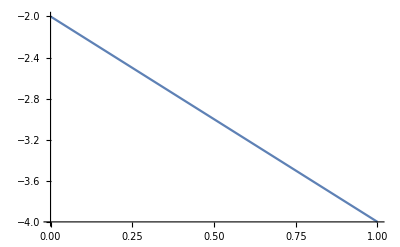

```mathematica
Plot[((2 x^2-2)/(1-x)),{x, 0, 1}]
```

```mathematica
n
```

n

```mathematica
Solve[11-2/3 nf == 0, nf]
```

{{nf→33/2}}